## Cálculo e Equações Diferenciais

Derivadas

Integrais

Séries de Taylor

Solução de Equações Lineares e Não Lineares

Solução de Equações Diferencias Ordinárias

Solução de Equações Diferenciais Parciais

◀     |     ▶

## Derivadas

Temos duas formas de calcular Derivadas:

f '

D[f,x]

```mathematica
f[x_]:=x^2+3;
```

```mathematica
f'[x]
D[f[x],x]
```

2 x

2 x

◀     |     ▶

## Derivadas de Alta Ordem

```mathematica
g[x_,y_]:=Cos[x^2-3y^3];
D[g[x,y],{x,3}]
D[g[x,y],{x,4},{y,2}]
```

-12 x Cos[x^2-3 y^3]+8 x^3 Sin[x^2-3 y^3]

-12 (-81 y^4 Cos[x^2-3 y^3]+18 y Sin[x^2-3 y^3])+16 x^4 (-81 y^4 Cos[x^2-3 y^3]+18 y Sin[x^2-3 y^3])+48 x^2 (-18 y Cos[x^2-3 y^3]-81 y^4 Sin[x^2-3 y^3])

◀     |     ▶

## Derivadas em um Ponto

```mathematica
D[f[x],{x}]/.{x->1}
```

2

Isto é equivalente à calcular

(∂f(x))/(∂x)|_(x=0.5)

◀     |     ▶

## Gráficos de Derivadas

```mathematica
h[x_]=Cos[x];
Plot[D[h[x],x],{x,0,π}]
```

General::ivar: 0.0000641782 is not a valid variable.

General::ivar: 0.0641783 is not a valid variable.

General::ivar: 0.128292 is not a valid variable.

General::stop: Further output of General :: "ivar" will be suppressed during this calculation.

-Graphics-

Por que isto ocorre?

◀     |     ▶

## Gráficos de Derivadas

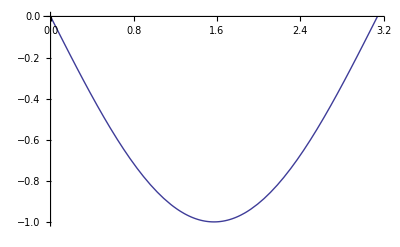

```mathematica
Plot[D[h[x],x]/.x->y,{y,0,π}]
```

◀     |     ▶

## Exercício

Faça o gráfico da função h e de suas derivadas de ordem 1 até 7.

◀     |     ▶

## Integrais

Para calcular integrais usamos:

```mathematica
Integrate[Cos[x],x] (* Indefinida *)
```

Sin[x]

```mathematica
Integrate[Cos[x],{x,0,2}] (* Definida *)
```

Sin[2]

```mathematica
Integrate[Cos[x]*Sin[y],x,y]
```

-Cos[y] Sin[x]

◀     |     ▶

## Integração Numérica

Em geral não conseguimos calcular integrais de forma simbólica. Nestes casos devemos recorrer a cálculos numéricos.

```mathematica
NIntegrate[Log[x]/x,{x,1,100}]
```

10.6038

◀     |     ▶

## Integrações Legais

```mathematica
Clear[a]
Integrate[Boole[x^2+y^2<a],{x,0,1},{y,0,1}]
```

Piecewise[{{1, a≥2}, {(a π)/4, 0<a≤1}, {1/2 (2 √(-1+a)+a ArcCsc[√a]-a ArcTan[√(-1+a)]), 1<a<2}}]

```mathematica
Table[RegionPlot[x^2+y^2<a,{x,0,1},{y,0,1},FrameTicks->None],{a,{1/2,3/2,5/2}}]
```

## Exercício

Calcule a área mais densa da Figura abaixo. Os círculos
posseum raio 2 e seus centros estão localizados 
em um triângulo equilátero de lado 2.

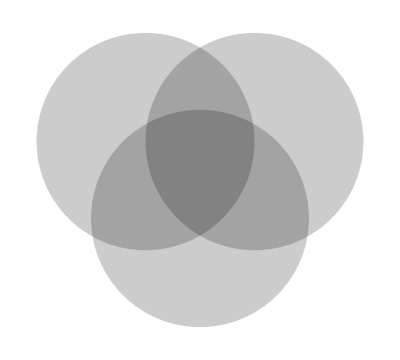

◀     |     ▶

## Séries de Taylor

O Mathematica permite o cálculo de séries de taylor centradas em um ponto qualquer:

```mathematica
Series[ArcTan[x],{x,0,7}]
```

x-x^3/3+x^5/5-x^7/7+O[x]^8

```mathematica
Normal[%]
```

x-x^3/3+x^5/5-x^7/7

◀     |     ▶

## Exercícios

Use a série de Taylor do ArcTan para encontrar uma série que determina o valor de π. Estime a dependência 
do erro com a ordem da série, comparando o valor conhecido de π.

◀     |     ▶

## Resolvendo Equações

```mathematica
Solve[2*x+3*y==2,x]
```

{{x→1/2 (2-3 y)}}

```mathematica
Solve[x^3+p*x+q==0,x]
```

{{x→-((2/3)^(1/3) p)/((-9 q+√3 √(4 p^3+27 q^2))^(1/3))+((-9 q+√3 √(4 p^3+27 q^2))^(1/3))/(2^(1/3) 3^(2/3))},{x→((1+ⅈ √3) p)/(2^(2/3) 3^(1/3) (-9 q+√3 √(4 p^3+27 q^2))^(1/3))-((1-ⅈ √3) (-9 q+√3 √(4 p^3+27 q^2))^(1/3))/(2 2^(1/3) 3^(2/3))},{x→((1-ⅈ √3) p)/(2^(2/3) 3^(1/3) (-9 q+√3 √(4 p^3+27 q^2))^(1/3))-((1+ⅈ √3) (-9 q+√3 √(4 p^3+27 q^2))^(1/3))/(2 2^(1/3) 3^(2/3))}}

```mathematica
Solve[x Sin[x]==1,x]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[x Sin[x]==1,x]

◀     |     ▶

## Métodos Numéricos

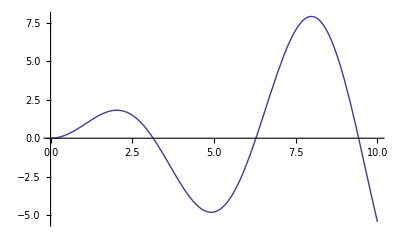

```mathematica
Plot[x Sin[x],{x,0,10}]
```

```mathematica
FindRoot[x Sin[x],{x,2.5}]
```

{x→3.14159}

◀     |     ▶

## Encontrando Mínimos

```mathematica
FindMinimum[x Sin[x],{x,4}]
```

{-4.81447,{x→4.91318}}

◀     |     ▶

## Exercício

Um salva-vidas nada duas vezes mais devagar do que corre. Ele deve resgatar a Pamela Anderson que está se afogando (discuta se isso é fisicamente possível).  Considere o gráfico abaixo:

Determine a trajetória que vai minimizar o tempo para o resgate da Pâmela Anderson. Considere apenas trajetórias lineares por partes.

```mathematica
FindMinimum[{d*e,2*d+2*e==4},{d,e}]
```

{1.,{d→1.,e→1.}}

◀     |     ▶

## Exercício

Considere a função de onda:

Se x<0  ψ_I=Exp(-ikx)+R Exp(i k x)     
 0<x<a  ψ_II(x) =A Exp(-q x) +B Exp(q x) 
 x>a ψ_III=T Exp(ikx)

Imponha as codições que a Função de onda e sua derivada sejam contínuas em todos os pontos e determine R, T, A e B em função de k e q.

◀     |     ▶

## Equações Diferenciais

```mathematica
DSolve[D[y[x],x]==(y[x])^2,y[x],x]
```

{{y[x]→1/(-x-C[1])}}

```mathematica
sol=DSolve[{D[y[x],x]==(y[x])^2,y[5]==10},y[x],x]
```

{{y[x]→-10/(-51+10 x)}}

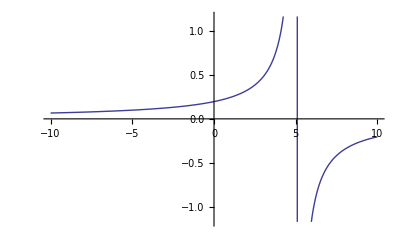

```mathematica
Plot[y[x]/.sol,{x,-10,10}]
```

◀     |     ▶

## Foguete com massa variável

dp/dt=v dm/dt+m dv/dt=-k/x^2-γ v
dm/dt=-m
dx/dt=v

-m

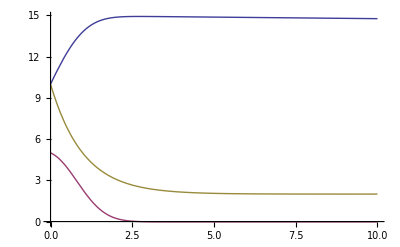

```mathematica
k=50;
γ=10;
Clear[x,v,m]
sol=NDSolve[{v[t] D[m[t],t]+m[t] D[v[t],t]==-k/(x[t])^2-γ*v[t],D[m[t],t]==-1*m[t]+2,
D[x[t],t]==v[t],x[0]==10,m[0]==10,v[0]==5},{v[t],m[t],x[t]},{t,0,100}]
Plot[{x[t]/.sol,v[t]/.sol,m[t]/.sol},{t,0,10}]
```

◀     |     ▶

## Exercício

Use a Função Manipulate para interagir dinamicamente com a solução da equação diferencial.

◀     |     ▶

## Exercício

Considere uma esfera de raio a de densidade ρ_e  imersa em água. A esfera é deslocada de su ponto de equilíbrio  e começa a oscilar. Escreva a equação diferencial que carcteriza esse movimento. Desenvolva um aplicativo que permite variar a condição inicial. Estudo o sistema no regime de pequenas perturbações e calcule a freqencia de oscilação nesse caso. Considere  uma bola de ping-pong como exemplo.

## Equações Diferenciais Parciais

```mathematica
sol2=NDSolve[{D[u[t,x], t,t]==D[u[t,x], x,x],u[0,x]==x*(1-x),Derivative[1,0][u][0,x]==0,u[t,0]==0,u[t,1]==0},u,{t,0,10},{x,0,1}];
Animate[Plot[(u[t,x]/.sol2),{x,0,1},PlotRange->{-0.5,0.5}],{t,0,10}]
```

NDSolve::eerr: Warning: Scaled local spatial error estimate of 953.778 at t = 10. in the direction of independent variable x is much greater than prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

```mathematica
sol=NDSolve[{D[u[t,x], t]==D[u[t,x], x,x],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u,{t,0,15},{x,0,5}];
Animate[Plot[(u[t,x]/.sol),{x,0,5},PlotRange->{-3,3}],{t,0,15}]
```

◀     |     ▶